# Lab report 8 – Data processing

Initialise ErrorBarPlots`

```mathematica
Needs["ErrorBarPlots`"]
```

## Data

```mathematica
processedData1 = {
{
{0.0227,0.0667},
ErrorBar[0.0002,0.0004]
}, {
{0.0263,0.0625},
ErrorBar[0.0002,0.0004]
}, {
{0.0294,0.0588},
ErrorBar[0.0003,0.0003]
}, {
{0.324,0.0556},
ErrorBar[0.0003,0.0003]
}, {
{0.0348,0.0526},
ErrorBar[0.0004,0.0003]
}, {
{0.0373,0.0500},
ErrorBar[0.0004,0.0003]
}, {
{0.0394,0.0476},
ErrorBar[0.0005,0.0002]
}, {
{0.0415,0.0456},
ErrorBar[0.0005,0.0002]
}
}
```

{{{0.0227,0.0667},ErrorBar[0.0002,0.0004]},{{0.0263,0.0625},ErrorBar[0.0002,0.0004]},{{0.0294,0.0588},ErrorBar[0.0003,0.0003]},{{0.324,0.0556},ErrorBar[0.0003,0.0003]},{{0.0348,0.0526},ErrorBar[0.0004,0.0003]},{{0.0373,0.05},ErrorBar[0.0004,0.0003]},{{0.0394,0.0476},ErrorBar[0.0005,0.0002]},{{0.0415,0.0456},ErrorBar[0.0005,0.0002]}}

```mathematica
processedData2 = {
{
{59.0,660},
ErrorBar[0.2,9]
}, {
{54.1,610},
ErrorBar[0.2,9]
}, {
{51.0,578},
ErrorBar[0.2,9]
}, {
{48.9,556},
ErrorBar[0.2,9]
}, {
{47.7,545},
ErrorBar[0.2,9]
}, {
{46.8,536},
ErrorBar[0.2,9]
}, {
{46.4,533},
ErrorBar[0.2,9]
}, {
{46.1,530},
ErrorBar[0.2,9]
}
}
```

{{{59.,660},ErrorBar[0.2,9]},{{54.1,610},ErrorBar[0.2,9]},{{51.,578},ErrorBar[0.2,9]},{{48.9,556},ErrorBar[0.2,9]},{{47.7,545},ErrorBar[0.2,9]},{{46.8,536},ErrorBar[0.2,9]},{{46.4,533},ErrorBar[0.2,9]},{{46.1,530},ErrorBar[0.2,9]}}

Defining some linear equations for both y-intercept and gradient method

Plotting errors for both methods

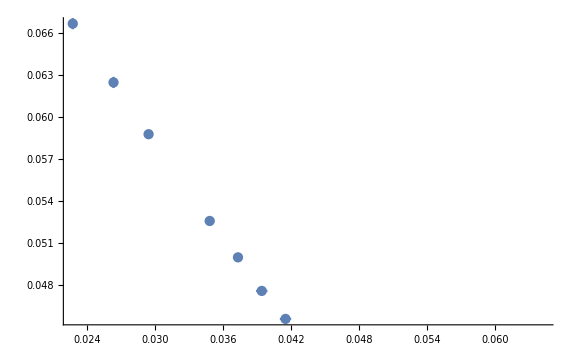

```mathematica
error1 = ErrorListPlot[processedData1,ImageSize->Large]
```

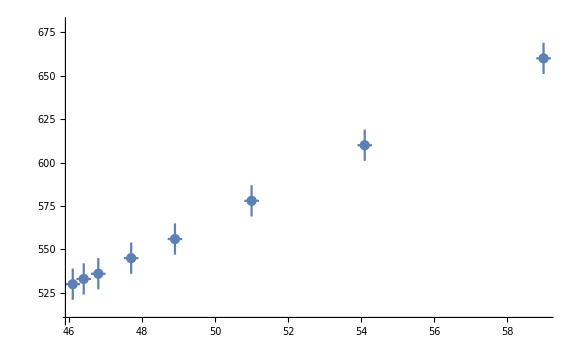

```mathematica
error2 = ErrorListPlot[processedData2, ImageSize->Large, PlotRange->{510,680}]
```

```mathematica
best1= ,
max1= ,
min1=
```

```mathematica
best2= ,
max2 = ,
min2 =
```

```mathematica
line1 = Plot[best1, min1, max1,{x, 0.02, 0.045}]
line2= Plot[best2, min2, max2, {x, 45.9, 59.2}]
```